```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults},numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},datafitParams={fitParams[[1,j]],fitParams[[2,j]],fitParams[[3,j]]};
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/Esigmasq];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari,Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];


modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-2, bNum->even}],{etav, bL, bT,data}];
dataforfit=Select[dataforfit,#[[1]]>6& ];
dataforfit=Select[dataforfit,(#[[2]]^2+#[[3]]^2)>9& ];
(*modelfitA2B[x1_,x2_,{a_,b_,c_, d_}]:=(a/(((x1^2)+(b*(x2^2))+c)^(d)));
fitJK =JackknifeFit3D[dataforfit,modelfitA2B[bL,bT,{a,b,c,d}],{a,b, c,d},{bL,bT}, modelfitA2B]*)
```

```mathematica
dataforfit
```

{{7,0,4,⟨0.01414(98)⟩_(RowBox[{)},{7,0,5,⟨0.00811(91)⟩_(RowBox[{)},{7,0,6,⟨0.00449(82)⟩_(RowBox[{)},{7,0,7,⟨0.00349(76)⟩_(RowBox[{)},{7,0,-4,⟨0.0126(11)⟩_(RowBox[{)},{7,0,-5,⟨0.00663(95)⟩_(RowBox[{)},{7,0,-6,⟨0.00378(88)⟩_(RowBox[{)},{7,0,-7,⟨0.00195(81)⟩_(RowBox[{)},{7,3,3,⟨0.01000(69)⟩_(RowBox[{)},{7,4,4,⟨0.00282(61)⟩_(RowBox[{)},{7,5,5,⟨0.00143(53)⟩_(RowBox[{)},{7,2,4,⟨0.01001(70)⟩_(RowBox[{)},{7,3,6,⟨0.00185(59)⟩_(RowBox[{)},{7,4,2,⟨0.01029(72)⟩_(RowBox[{)},{7,6,3,⟨0.00119(66)⟩_(RowBox[{)},{7,4,1,⟨0.01398(75)⟩_(RowBox[{)},{7,8,2,⟨0.00009 ± 0.00054⟩_(RowBox[{)},{7,3,-3,⟨0.01038(68)⟩_(RowBox[{)},{7,4,-4,⟨0.00409(58)⟩_(RowBox[{)},{7,5,-5,⟨0.00160(51)⟩_(RowBox[{)},{7,2,-4,⟨0.00887(72)⟩_(RowBox[{)},{7,3,-6,⟨0.00182(57)⟩_(RowBox[{)},{7,4,-2,⟨0.00980(70)⟩_(RowBox[{)},{7,6,-3,⟨0.00201(58)⟩_(RowBox[{)},{7,4,-1,⟨0.01280(73)⟩_(RowBox[{)},{7,8,-2,⟨800(560) × 10⟩_(RowBox[{)},{7,-3,3,⟨0.01000(69)⟩_(RowBox[{)},{7,-4,4,⟨0.00282(61)⟩_(RowBox[{)},{7,-5,5,⟨0.00143(53)⟩_(RowBox[{)},{7,-2,4,⟨0.01001(70)⟩_(RowBox[{)},{7,-3,6,⟨0.00185(59)⟩_(RowBox[{)},{7,-4,2,⟨0.01029(72)⟩_(RowBox[{)},{7,-6,3,⟨0.00119(66)⟩_(RowBox[{)},{7,-4,1,⟨0.01398(75)⟩_(RowBox[{)},{7,-8,2,⟨0.00009 ± 0.00054⟩_(RowBox[{)},{7,-3,-3,⟨0.01038(68)⟩_(RowBox[{)},{7,-4,-4,⟨0.00409(58)⟩_(RowBox[{)},{7,-5,-5,⟨0.00160(51)⟩_(RowBox[{)},{7,-2,-4,⟨0.00887(72)⟩_(RowBox[{)},{7,-3,-6,⟨0.00182(57)⟩_(RowBox[{)},{7,-4,-2,⟨0.00980(70)⟩_(RowBox[{)},{7,-6,-3,⟨0.00201(58)⟩_(RowBox[{)},{7,-4,-1,⟨0.01280(73)⟩_(RowBox[{)},{8,0,4,⟨0.00920(85)⟩_(RowBox[{)},{8,0,5,⟨0.00462(80)⟩_(RowBox[{)},{8,0,6,⟨0.00248(74)⟩_(RowBox[{)},{8,0,7,⟨0.00263(70)⟩_(RowBox[{)},{8,0,-4,⟨0.00684(92)⟩_(RowBox[{)},{8,0,-5,⟨0.00321(80)⟩_(RowBox[{)},{8,0,-6,⟨0.00235(75)⟩_(RowBox[{)},{8,0,-7,⟨0.00126(70)⟩_(RowBox[{)},{8,3,3,⟨0.00560(61)⟩_(RowBox[{)},{8,4,4,⟨850(550) × 10⟩_(RowBox[{)},{8,5,5,⟨450(470) × 10⟩_(RowBox[{)},{8,2,4,⟨0.00639(63)⟩_(RowBox[{)},{8,3,6,⟨470(520) × 10⟩_(RowBox[{)},{8,4,2,⟨0.00582(64)⟩_(RowBox[{)},{8,6,3,⟨670(630) × 10⟩_(RowBox[{)},{8,4,1,⟨0.00816(65)⟩_(RowBox[{)},{8,8,2,⟨720(500) × 10⟩_(RowBox[{)},{8,3,-3,⟨0.00590(61)⟩_(RowBox[{)},{8,4,-4,⟨0.00223(50)⟩_(RowBox[{)},{8,5,-5,⟨940(440) × 10⟩_(RowBox[{)},{8,2,-4,⟨0.00472(64)⟩_(RowBox[{)},{8,3,-6,⟨810(500) × 10⟩_(RowBox[{)},{8,4,-2,⟨0.00528(63)⟩_(RowBox[{)},{8,6,-3,⟨0.00104(52)⟩_(RowBox[{)},{8,4,-1,⟨0.00755(66)⟩_(RowBox[{)},{8,8,-2,⟨230(480) × 10⟩_(RowBox[{)},{8,-3,3,⟨0.00560(61)⟩_(RowBox[{)},{8,-4,4,⟨850(550) × 10⟩_(RowBox[{)},{8,-5,5,⟨450(470) × 10⟩_(RowBox[{)},{8,-2,4,⟨0.00639(63)⟩_(RowBox[{)},{8,-3,6,⟨470(520) × 10⟩_(RowBox[{)},{8,-4,2,⟨0.00582(64)⟩_(RowBox[{)},{8,-6,3,⟨670(630) × 10⟩_(RowBox[{)},{8,-4,1,⟨0.00816(65)⟩_(RowBox[{)},{8,-8,2,⟨720(500) × 10⟩_(RowBox[{)},{8,-3,-3,⟨0.00590(61)⟩_(RowBox[{)},{8,-4,-4,⟨0.00223(50)⟩_(RowBox[{)},{8,-5,-5,⟨940(440) × 10⟩_(RowBox[{)},{8,-2,-4,⟨0.00472(64)⟩_(RowBox[{)},{8,-3,-6,⟨810(500) × 10⟩_(RowBox[{)},{8,-4,-2,⟨0.00528(63)⟩_(RowBox[{)},{8,-6,-3,⟨0.00104(52)⟩_(RowBox[{)},{8,-4,-1,⟨0.00755(66)⟩_(RowBox[{)},{9,0,4,⟨0.00520(77)⟩_(RowBox[{)},{9,0,5,⟨0.00253(71)⟩_(RowBox[{)},{9,0,6,⟨0.00101(68)⟩_(RowBox[{)},{9,0,7,⟨0.00142(64)⟩_(RowBox[{)},{9,0,-4,⟨0.00349(80)⟩_(RowBox[{)},{9,0,-5,⟨0.00181(72)⟩_(RowBox[{)},{9,0,-6,⟨0.00112(68)⟩_(RowBox[{)},{9,0,-7,⟨570(650) × 10⟩_(RowBox[{)},{9,3,3,⟨0.00224(54)⟩_(RowBox[{)},{9,4,4,⟨570(470) × 10⟩_(RowBox[{)},{9,5,5,⟨500(430) × 10⟩_(RowBox[{)},{9,2,4,⟨0.00359(56)⟩_(RowBox[{)},{9,3,6,⟨4.×10^-6 ± 0.00047⟩_(RowBox[{)},{9,4,2,⟨0.00283(57)⟩_(RowBox[{)},{9,6,3,⟨540(560) × 10⟩_(RowBox[{)},{9,4,1,⟨0.00439(58)⟩_(RowBox[{)},{9,8,2,⟨560(450) × 10⟩_(RowBox[{)},{9,3,-3,⟨0.00338(55)⟩_(RowBox[{)},{9,4,-4,⟨0.00122(45)⟩_(RowBox[{)},{9,5,-5,⟨0.00004 ± 0.0004⟩_(RowBox[{)},{9,2,-4,⟨0.00254(55)⟩_(RowBox[{)},{9,3,-6,⟨840(450) × 10⟩_(RowBox[{)},{9,4,-2,⟨0.00277(57)⟩_(RowBox[{)},{9,6,-3,⟨350(460) × 10⟩_(RowBox[{)},{9,4,-1,⟨0.00387(59)⟩_(RowBox[{)},{9,8,-2,⟨-0.00008 ± 0.00046⟩_(RowBox[{)},{9,-3,3,⟨0.00224(54)⟩_(RowBox[{)},{9,-4,4,⟨570(470) × 10⟩_(RowBox[{)},{9,-5,5,⟨500(430) × 10⟩_(RowBox[{)},{9,-2,4,⟨0.00359(56)⟩_(RowBox[{)},{9,-3,6,⟨4.×10^-6 ± 0.00047⟩_(RowBox[{)},{9,-4,2,⟨0.00283(57)⟩_(RowBox[{)},{9,-6,3,⟨540(560) × 10⟩_(RowBox[{)},{9,-4,1,⟨0.00439(58)⟩_(RowBox[{)},{9,-8,2,⟨560(450) × 10⟩_(RowBox[{)},{9,-3,-3,⟨0.00338(55)⟩_(RowBox[{)},{9,-4,-4,⟨0.00122(45)⟩_(RowBox[{)},{9,-5,-5,⟨0.00004 ± 0.0004⟩_(RowBox[{)},{9,-2,-4,⟨0.00254(55)⟩_(RowBox[{)},{9,-3,-6,⟨840(450) × 10⟩_(RowBox[{)},{9,-4,-2,⟨0.00277(57)⟩_(RowBox[{)},{9,-6,-3,⟨350(460) × 10⟩_(RowBox[{)},{9,-4,-1,⟨0.00387(59)⟩_(RowBox[{)},{10,0,4,⟨0.00341(72)⟩_(RowBox[{)},{10,0,5,⟨0.00183(67)⟩_(RowBox[{)},{10,0,6,⟨0.00101(63)⟩_(RowBox[{)},{10,0,7,⟨900(620) × 10⟩_(RowBox[{)},{10,0,-4,⟨0.00121(75)⟩_(RowBox[{)},{10,0,-5,⟨570(670) × 10⟩_(RowBox[{)},{10,0,-6,⟨220(640) × 10⟩_(RowBox[{)},{10,0,-7,⟨770(630) × 10⟩_(RowBox[{)},{10,3,3,⟨0.00147(51)⟩_(RowBox[{)},{10,4,4,⟨110(460) × 10⟩_(RowBox[{)},{10,5,5,⟨280(410) × 10⟩_(RowBox[{)},{10,2,4,⟨0.00236(53)⟩_(RowBox[{)},{10,3,6,⟨0.00003 ± 0.00043⟩_(RowBox[{)},{10,4,2,⟨0.00168(54)⟩_(RowBox[{)},{10,6,3,⟨120(500) × 10⟩_(RowBox[{)},{10,4,1,⟨0.00275(54)⟩_(RowBox[{)},{10,8,2,⟨5.×10^-6 ± 0.00041⟩_(RowBox[{)},{10,3,-3,⟨0.00170(50)⟩_(RowBox[{)},{10,4,-4,⟨540(430) × 10⟩_(RowBox[{)},{10,5,-5,⟨-380(390) × 10⟩_(RowBox[{)},{10,2,-4,⟨0.00151(51)⟩_(RowBox[{)},{10,3,-6,⟨570(440) × 10⟩_(RowBox[{)},{10,4,-2,⟨0.00111(51)⟩_(RowBox[{)},{10,6,-3,⟨200(450) × 10⟩_(RowBox[{)},{10,4,-1,⟨0.00212(55)⟩_(RowBox[{)},{10,8,-2,⟨-0.00006 ± 0.00042⟩_(RowBox[{)},{10,-3,3,⟨0.00147(51)⟩_(RowBox[{)},{10,-4,4,⟨110(460) × 10⟩_(RowBox[{)},{10,-5,5,⟨280(410) × 10⟩_(RowBox[{)},{10,-2,4,⟨0.00236(53)⟩_(RowBox[{)},{10,-3,6,⟨0.00003 ± 0.00043⟩_(RowBox[{)},{10,-4,2,⟨0.00168(54)⟩_(RowBox[{)},{10,-6,3,⟨120(500) × 10⟩_(RowBox[{)},{10,-4,1,⟨0.00275(54)⟩_(RowBox[{)},{10,-8,2,⟨5.×10^-6 ± 0.00041⟩_(RowBox[{)},{10,-3,-3,⟨0.00170(50)⟩_(RowBox[{)},{10,-4,-4,⟨540(430) × 10⟩_(RowBox[{)},{10,-5,-5,⟨-380(390) × 10⟩_(RowBox[{)},{10,-2,-4,⟨0.00151(51)⟩_(RowBox[{)},{10,-3,-6,⟨570(440) × 10⟩_(RowBox[{)},{10,-4,-2,⟨0.00111(51)⟩_(RowBox[{)},{10,-6,-3,⟨200(450) × 10⟩_(RowBox[{)},{10,-4,-1,⟨0.00212(55)⟩_(RowBox[{)}}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,b_,c_}]:=((a*Exp[-b*x2^2])^x1)*Exp[-c*x3^2];
fitJK =JackknifeFit4D[dataforfit,modelfitA2B[n, bL,bT,{a,b, c}],{{a, 0.6437557},{b, 0.0111032027476537},{c, 0.0730360083780625}},{n,bL,bT}, modelfitA2B];
Print[fitJK //OutputForm]
```

{FitParameters -> {⟨0.6269(93)⟩_(2902J), ⟨0.00924(94)⟩_(2902J), ⟨0.0730(66)⟩_(2902J)}, chisquareDoF -> 1.17365}

```mathematica
fitparavalues =FitParameters/. fitJK;
Print[fitparavalues[[2]]*9//OutputForm]
```

⟨0.0831(85)⟩_(2902J)

```mathematica
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-2, bNum->even}],{etav, bL, bT,data}];
dataforfit=Select[dataforfit,#[[1]]>6& ];
dataforfit=Select[dataforfit,(#[[2]]^2+#[[3]]^2)>9& ];
modelfitA2B[x1_,x2_, x3_,{a_,b_,c_}]:=((a*Exp[-b*x2^2])^x1)*Exp[-c*x3^2];
fitJK =JackknifeFit4D[dataforfit,modelfitA2B[n, bL,bT,{a,b, c}],{{a, 0.6437557},{b, 0.0111032027476537},{c, 0.0730360083780625}},{n,bL,bT}, modelfitA2B];
Print[fitJK //OutputForm]
```

{FitParameters -> {⟨-0.434(12)⟩_(2902J), ⟨0.0088(24)⟩_(2902J), ⟨0.0375(76)⟩_(2902J)}, chisquareDoF -> 3.13854}

```mathematica
FitAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
(*dataforfit=Select[fulldataforfit,#[[2]]<2&&#[[2]]>-2& ];*)
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c, d}],{a,b, c, d},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
(*Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];*)
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into"  ,ampname," -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
(*Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];*)
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->even}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]]

(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];
Print[fitPlotbL]*)
(*Export["/Users/hariprashadravikumar/Downloads/Pbfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->even}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}]];
fitPBbandforallbP = {};
Do[
fitb2band = {};
Do[
AppendTo[fitb2band,{bsqx, modelfitJackkifband[modelfit, fitParas,bsqx,Pb32by2Pilist[[Pbi]]]}];
,{bsqx,1,68,1}];
AppendTo[fitPBbandforallbP,fitb2band];
,{Pbi,Length[Pb32by2Pilist]}];
fitPlotbsq=Show[Plotbsq,Table[ErrorListPlot[MakeErrBars[fitPBbandforallbP[[Pbii]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[Pbii,15]]],0.5],Joined->True],{Pbii,Length[Pb32by2Pilist]}]];
(*fitPlotbsq=Show[Table[Plot[modelfitJackkife[modelfit, fitParas, Pb32by2Pilist[[Pbi]],bsqx][[1]],{bsqx,Min[bsquarelist],Max[bsquarelist]},PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[Mod[Pbi,15]]]],{Pbi,Length[Pb32by2Pilist]}],Plotbsq];*)
Print[fitPlotbsq];
Export["/Users/hariprashadravikumar/Downloads/bsqfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbsq,"PDF",ImageResolution->600];*)
)
FitImAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
(*Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]/P1],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];*)
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->odd}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]];
(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];*)
Print[fitPlotbL]
)
```

Re A12B =>  = -1 ,eta = 8
 Fitting intoA12B -> () = {⟨-0.222(49)⟩_(2902J), ⟨3.29(64)⟩_(2902J), ⟨0.44(17)⟩_(2902J)}
 chisquareDoF = 1.39353

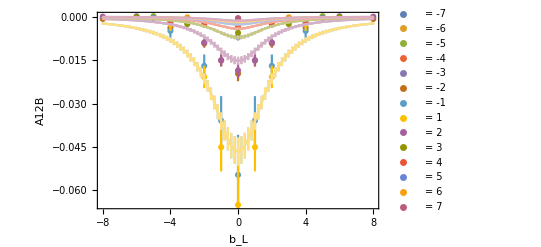

```mathematica
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
FitAfordiffbLbT[A12B, -1, 8, modelfitA12B]
```

Re A2B =>  = -1 ,eta = 8
 Fitting intoA2B -> () = {⟨1.389(20)⟩_(2902J), ⟨1.138(12)⟩_(2902J), ⟨1.600(14)⟩_(2902J)}
 chisquareDoF = 1.5287

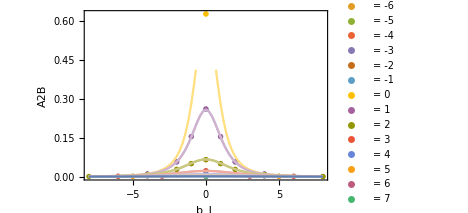

```mathematica
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=(a/(((x1^2)+(b*(x2^2))+c)^1.67));
FitAfordiffbLbT[A2B, -1, 8, modelfitA2B]
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.071(12)⟩_(2902J), ⟨1.18(17)⟩_(2902J), ⟨2.99(59)⟩_(2902J)}
 chisquareDoF = 1.43998

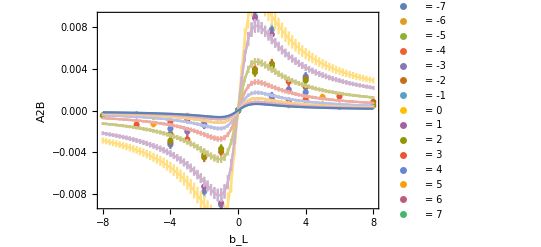

```mathematica
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
FitImAfordiffbLbT[A2B, -1, 8, modelfitImA2B]
```

```mathematica
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]]
aa = MakeErrBars[{{1,MassN}}][[1,1,2]]
```

⟨0.6228(28)⟩_(RowBox[{)

0.622814

```mathematica
modelReA12BNfou[pb_]:=aa*1/(aa+((pb^2)/(-1^2)))*1/(aa+(9-((pb^2)/(-1^2))));
NFourierTransform[modelReA12BNfou[pb],pb,0.1]//Re
```

-0.00270471

```mathematica
SiversShiftNoErrbars[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];

modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=(a/(((x1^2)+(b*(x2^2))+c)^1.67));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =MakeErrBars[{{1,fitParasA12B[[1]]}}][[1,1,2]];
fitbA12B=MakeErrBars[{{1,fitParasA12B[[2]]}}][[1,1,2]];
fitcA12B =MakeErrBars[{{1,fitParasA12B[[3]]}}][[1,1,2]];
fitaA2B =MakeErrBars[{{1,fitParasA2B[[1]]}}][[1,1,2]];
fitbA2B=MakeErrBars[{{1,fitParasA2B[[2]]}}][[1,1,2]];
fitcA2B =MakeErrBars[{{1,fitParasA2B[[3]]}}][[1,1,2]];
fitaImA2B =MakeErrBars[{{1,fitParasImA2B[[1]]}}][[1,1,2]];
fitbImA2B=MakeErrBars[{{1,fitParasImA2B[[2]]}}][[1,1,2]];
fitcImA2B =MakeErrBars[{{1,fitParasImA2B[[3]]}}][[1,1,2]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
fourieReA2Bxforplot={};
fourieImA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_]:=fitaA12B*1/(fitbA12B+((pb^2)/(P1^2)))*1/(fitcA12B+(b2-((pb^2)/(P1^2))));
modelReA2BNfou[pb_]:=fitaA2B*1/((((pb^2)/(P1^2))+(fitbA2B*(b2-((pb^2)/(P1^2))))+fitcA2B)^1.67);
modelImA2BNfou[pb_]:=fitaImA2B*((pb)/(-P1))*1/(fitbImA2B+((pb^2)/(P1^2)))*1/(fitcImA2B+(b2-((pb^2)/(P1^2))));
fourierA12Bforx = Re[NFourierTransform[modelReA12BNfou[pb],pb,x]];
fourierREA2Bforx=Re[NFourierTransform[modelReA2BNfou[pb],pb,x]];
fourierIMA2Bforx=Im[NFourierTransform[modelImA2BNfou[pb],pb,x]];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,II*siversrforx}];
AppendTo[fourieA12Bxforplot,{x,II*fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,II*fourierA2Bforx}];
AppendTo[fourieReA2Bxforplot,{x,II*fourierREA2Bforx}];
AppendTo[fourieImA2Bxforplot,{x,II*fourierIMA2Bforx}];
,{x,0,1, 0.1}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.5;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];

MkErrReA2B=MakeErrBars[fourieReA2Bxforplot];
PlotfourieReA2Bx= ErrorListPlot[MkErrReA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];
Print[PlotfourieReA2Bx];
MkErrImA2B=MakeErrBars[fourieImA2Bxforplot];
PlotfourieImA2Bx= ErrorListPlot[MkErrImA2B,FrameLabel->{ ,Im }, Frame->True , PlotRange->Full];
Print[PlotfourieImA2Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

Fitting:    -> () = {⟨-0.222(49)⟩_(2902J), ⟨3.29(64)⟩_(2902J), ⟨0.44(17)⟩_(2902J)}, chisquareDoF = 1.39353
 Fitting:    -> () = {⟨1.389(20)⟩_(2902J), ⟨1.138(12)⟩_(2902J), ⟨1.600(14)⟩_(2902J)}, chisquareDoF = 1.5287
 Fitting:   -> () = {⟨0.071(12)⟩_(2902J), ⟨1.18(17)⟩_(2902J), ⟨2.99(59)⟩_(2902J)} chisquareDoF = 1.43998
  = 9  = -1 ,eta = 8

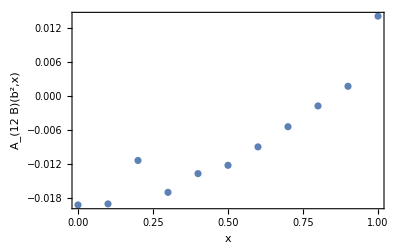

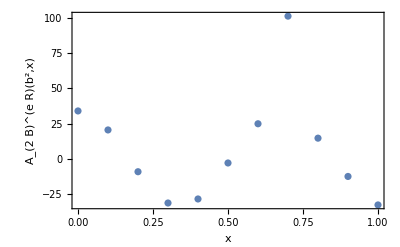

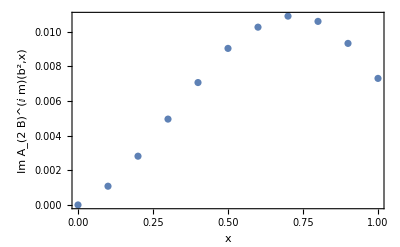

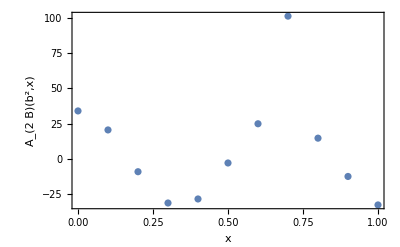

Sivers shift in GeV

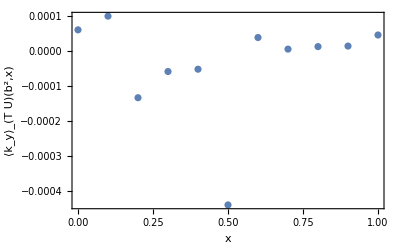

```mathematica
SiversShiftNoErrbars[9,-1, 8]
```

Fitting:    -> () = {⟨-0.120(25)⟩_(2902J), ⟨2.18(36)⟩_(2902J), ⟨-0.09 ± 0.1⟩_(2902J)}, chisquareDoF = 2.50832
 Fitting:    -> () = {⟨1.279(28)⟩_(2902J), ⟨1.272(20)⟩_(2902J), ⟨1.496(20)⟩_(2902J)}, chisquareDoF = 4.02094
 Fitting:   -> () = {⟨0.077(13)⟩_(2902J), ⟨0.95(14)⟩_(2902J), ⟨1.78(36)⟩_(2902J)} chisquareDoF = 1.65551
  = 9  = -2 ,eta = 8

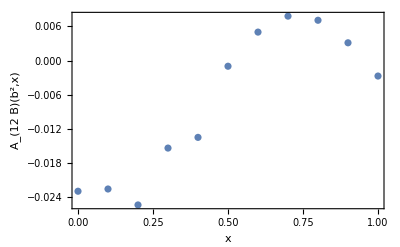

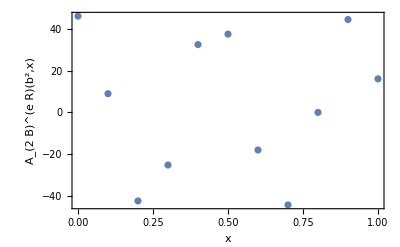

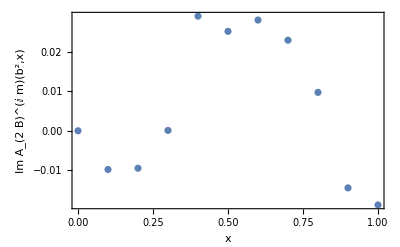

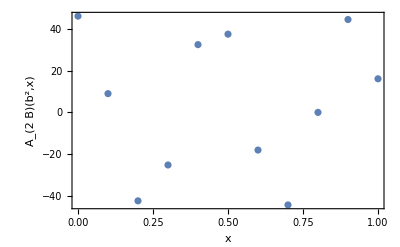

Sivers shift in GeV

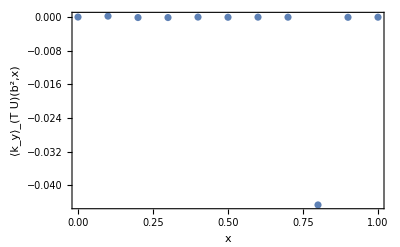

```mathematica
SiversShiftNoErrbars[9,-2, 8]
```

Fitting:    -> () = {⟨-0.061(30)⟩_(2902J), ⟨2.13(72)⟩_(2902J), ⟨-0.28(19)⟩_(2902J)}, chisquareDoF = 0.919706
 Fitting:    -> () = {⟨1.077(46)⟩_(2902J), ⟨1.360(38)⟩_(2902J), ⟨1.343(33)⟩_(2902J)}, chisquareDoF = 3.12326
 Fitting:   -> () = {⟨0.042(13)⟩_(2902J), ⟨0.76(20)⟩_(2902J), ⟨0.45(31)⟩_(2902J)} chisquareDoF = 0.60705
  = 9  = -3 ,eta = 8

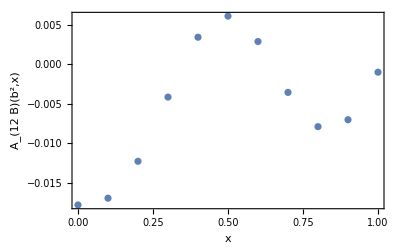

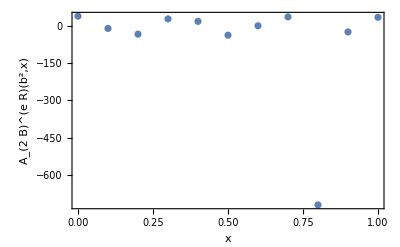

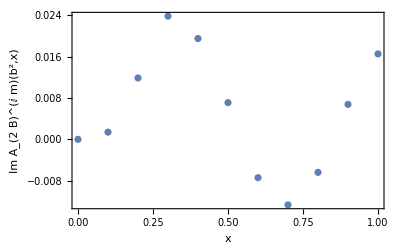

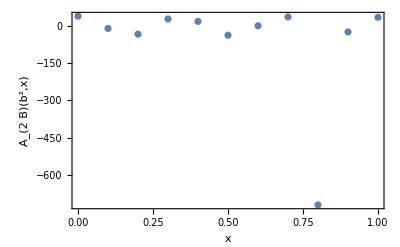

Sivers shift in GeV

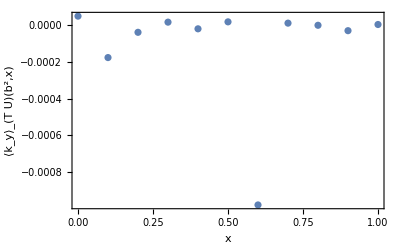

```mathematica
SiversShiftNoErrbars[9,-3, 8]
```

```mathematica
SiversShiftNoErrbars[9,-4, 8]
```

Fitting:    -> () =                3                                               6                                             3
{⟨-403(31) × 10 ⟩_(2902J), ⟨-3.60(20) × 10 ⟩_(2902J), ⟨-12(16) × 10 ⟩_(2902J)}, chisquareDoF = 4.27757
 Fitting:    -> () = {⟨0.925(89)⟩_(2902J), ⟨1.303(81)⟩_(2902J), ⟨1.194(61)⟩_(2902J)}, chisquareDoF = 1.57747
 Fitting:   -> () = {⟨0.026(21)⟩_(2902J), ⟨0.92(41)⟩_(2902J), ⟨-0.15(48)⟩_(2902J)} chisquareDoF = 0.492506
  = 9  = -4 ,eta = 8

$Aborted

```mathematica
NFourierTransformJK[modelReA12BNfou_,pb_,x_, FourierNum_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]]];
modelvalue=ParallelTable[FourierNum[NFourierTransform[modelReA12BNfou[pb, j],pb,x]],{j,100}];(*numFs -> 10 for now*)
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
SiversShift[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];

modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=(a/(((x1^2)+(b*(x2^2))+c)^1.67));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*1/(fitbA12B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA12B[[jknum]]+(b2-((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*1/((((pb^2)/(P1^2))+(fitbA2B[[jknum]]*(b2-((pb^2)/(P1^2))))+fitcA2B[[jknum]])^1.67);
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*1/(fitbImA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcImA2B[[jknum]]+(b2-((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.5;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

```mathematica
SiversShift[9,-1, 8]
```

$Aborted

```mathematica
SiversShift[9,-2, 8]
```

```mathematica
SiversShift[9,-3, 8]
```